```mathematica
RollSet[n_Integer]:=Module[
{},
Table[RandomInteger[{1,365}],{n}]
]
CheckSet[list_]:=Module[
{l1,l2},
l1 = Length[list];
l2 = Length[Tally[list]];
If[l1≠l2,1,0]
]
```

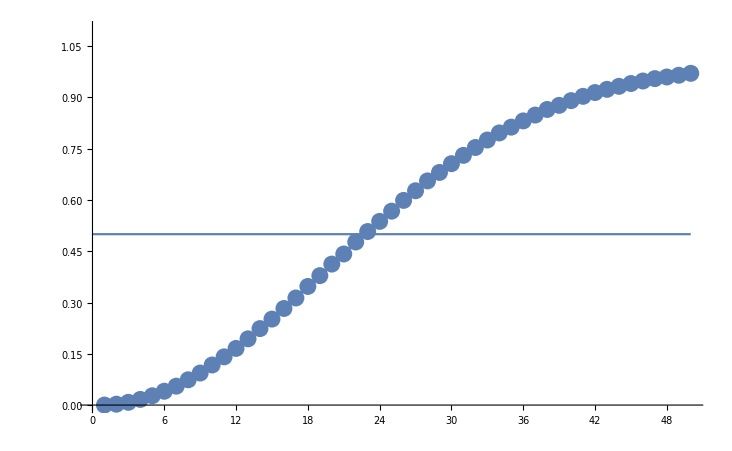

1 | 0.
2 | 0.00257
3 | 0.00802
4 | 0.01649
5 | 0.02716
6 | 0.04041
7 | 0.05523
8 | 0.07396
9 | 0.09372
10 | 0.11725
11 | 0.14109
12 | 0.16575
13 | 0.19376
14 | 0.22375
15 | 0.25154
16 | 0.28256
17 | 0.31334
18 | 0.34706
19 | 0.37868
20 | 0.41247
21 | 0.44205
22 | 0.47716
23 | 0.50777
24 | 0.53746
25 | 0.56735
26 | 0.59881
27 | 0.62703
28 | 0.65589
29 | 0.68064
30 | 0.70632
31 | 0.73062
32 | 0.75365
33 | 0.77552
34 | 0.79629
35 | 0.81318
36 | 0.83142
37 | 0.84849
38 | 0.86491
39 | 0.87689
40 | 0.89075
41 | 0.90333
42 | 0.9144
43 | 0.9238
44 | 0.9326
45 | 0.94081
46 | 0.94818
47 | 0.95515
48 | 0.95994
49 | 0.96498
50 | 0.97064

```mathematica
numRolls=100000;
ProgressIndicator[Dynamic[x],{1,numRolls}]
ProgressIndicator[Dynamic[y],{1,50}]
Data = Table[
x=i;
y=j;
CheckSet[RollSet[j]]
,{i,numRolls},{j,50}];
D2=Transpose[Data];
D3=Table[
{i,1.*Mean[D2⟦i⟧]}
,{i,Length[D2]}];
LP=ListPlot[D3];
LP2=ListLinePlot[D3];
halfmark = Plot[0.5,{x,0,50}];
Show[{LP,LP2,halfmark},PlotRange->{{0,50},{0,1.1}}]
D3//TableForm
```

```mathematica
Mean[Table[CheckSet[RollSet[300]],{i,100000}]]
```

1